# Gravitational Memory Test-Code

## Simon Thill 2025

All of the code in this document is purely for testing and development. The final code used in my thesis can be found at https://github.com/Simont12321/Gravitational-memory-thesis.

### To Do

- Redo +polarization in 3D with rotational about the correct axis of by rotating the polarization by ω. 
- Do a cross polarized wave in 3D.

### Variables and Functions and testing

```mathematica
ClearAll["Global`*"]
```

#### Rotation matrices applied to GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

Applying the rotation matrix to + polarization. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
```

#### Applying rotations:

Simplest case: Plus polarized wave rotated -α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].P.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(Cos[ϕ]^2-Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α]^2 Sin[ϕ] | -Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]
Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ] | -Cos[α]^2 Cos[ϕ] | Cos[α] Cos[ϕ]^2 Sin[α]-Sin[ϕ]^2
-Sin[α]^2 Sin[ϕ] | Cos[α] Sin[α] | -Cos[ϕ] Sin[α]^2)

The most complex case: GW with a general plus polarization p and cross polarisation x rotated α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].G.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(p Cos[ϕ]^2-x Cos[ϕ] (Cos[α]+Sin[α]) Sin[ϕ]-p Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α] (x Cos[ϕ]+p Cos[α] Sin[ϕ]) | -x Cos[ϕ]^2 Sin[α]-p Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]+x Cos[α] Sin[ϕ]^2
Cos[α] Cos[ϕ] (x Cos[ϕ]+p Sin[α] Sin[ϕ])+Sin[ϕ] (p Cos[ϕ]-x Sin[α] Sin[ϕ]) | Cos[α] (-p Cos[α] Cos[ϕ]+x Sin[ϕ]) | -Sin[ϕ] (x Cos[ϕ] Sin[α]+p Sin[ϕ])+Cos[α] Cos[ϕ] (p Cos[ϕ] Sin[α]-x Sin[ϕ])
-Sin[α] (x Cos[ϕ]+p Sin[α] Sin[ϕ]) | p Cos[α] Sin[α] | Sin[α] (-p Cos[ϕ] Sin[α]+x Sin[ϕ]))

#### Other variables

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP distance from GW source to photon
α angle between GW source and photon (measured up from GW propegation vector)
dP distance from Earth to the photon
tmin initial time the photon encounters the GW
n vector pointing to point on the sky where the photon is found

```mathematica
$Assumptions=dG>0&&h0>0&&tP>tG&&0<=θ<=2 π&&t∈Reals;
c= 1;
tG = 0;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
(*A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] *)
DP[tP_, t_] := c(tP-t)
(*DP[tP_, t_] := If[tP>t,c(tP-t), 0]*) (*solves for if tP > t, but shouldn't be needed, although it did change the ϵ and h expresions a little*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
TrigSimp[opp_, adj_] := FullSimplify[2*opp/Sqrt[adj^2+opp^2]*adj/Sqrt[adj^2+opp^2]] (*Simplifies Sin[2ArcTan[opp/adj]]*)(*Sin(2x) = 2CosxSinx*)
```

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
RP[dG,tP, t ,θ]
```

√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])

```mathematica
Simplify[RP[dG,tP, Tmin[tG, tP, dG,θ] ,θ] - Tmin[tG, tP, dG,θ] -dG]
```

0

```mathematica
A[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]-π]]
```

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, ϕ],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}]
```

```mathematica
B[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]-π]]
```

```mathematica
Manipulate[Labeled[Plot[Θ[dG,RP[dG,tP, t,θ], θ, ϕ],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}]
```

#### Testing functions

```mathematica
Simplify[({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}})/. t->tP-dP]
```

{{(dG-dP Cos[θ])^2/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2)),0,(dP (dG-dP Cos[θ]) Sin[θ])/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2))},{0,-1/(√(dG^2+dP^2-2 dG dP Cos[θ])),0},{(dP (dG-dP Cos[θ]) Sin[θ])/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2)),0,(dP^2 Sin[θ]^2)/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2))}}

```mathematica
MatrixForm[%52]
```

```mathematica
({{(dG-dP Cos[θ])^2/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2)), 0, (dP (dG-dP Cos[θ]) Sin[θ])/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2))}, {0, -1/(√(dG^2+dP^2-2 dG dP Cos[θ])), 0}, {(dP (dG-dP Cos[θ]) Sin[θ])/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2)), 0, (dP^2 Sin[θ]^2)/((dG^2+dP^2-2 dG dP Cos[θ])^(3/2))}})
```

```mathematica
MatrixForm[%50]
```

((dG+x Cos[θ])^2/((dG^2+x^2+2 dG x Cos[θ])^(3/2)) | 0 | -(x (dG+x Cos[θ]) Sin[θ])/((dG^2+x^2+2 dG x Cos[θ])^(3/2))
0 | -1/(√(dG^2+x^2+2 dG x Cos[θ])) | 0
-(x (dG+x Cos[θ]) Sin[θ])/((dG^2+x^2+2 dG x Cos[θ])^(3/2)) | 0 | (x^2 Sin[θ]^2)/((dG^2+x^2+2 dG x Cos[θ])^(3/2)))

```mathematica
Simplify[({{(dG+x Cos[θ])^2/((dG^2+x^2+2 dG x Cos[θ])^(3/2)), 0, -(x (dG+x Cos[θ]) Sin[θ])/((dG^2+x^2+2 dG x Cos[θ])^(3/2))}, {0, -1/(√(dG^2+x^2+2 dG x Cos[θ])), 0}, {-(x (dG+x Cos[θ]) Sin[θ])/((dG^2+x^2+2 dG x Cos[θ])^(3/2)), 0, (x^2 Sin[θ]^2)/((dG^2+x^2+2 dG x Cos[θ])^(3/2))}})/. t->x+tP]
```

```mathematica
Simplify[t-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])/. t->tP-dP]
```

-dP+tP+(tP (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])

```mathematica
TrigReduce[-dP+tP+(tP (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])]
```

(-2 dG dP+2 dG tP-2 dP tP+tP^2+2 dG dP Cos[θ])/(2 (dG+tP-dG Cos[θ]))

```mathematica
Cancel[(-2 dG dP+2 dG tP-2 dP tP+tP^2+2 dG dP Cos[θ])/(2 (dG+tP-dG Cos[θ]))]
```

(2 dG dP-2 dG tP+2 dP tP-tP^2-2 dG dP Cos[θ])/(2 (-dG-tP+dG Cos[θ]))

```mathematica
FullSimplify[(2 dG dP-2 dG tP+2 dP tP-tP^2-2 dG dP Cos[θ])/(2 (-dG-tP+dG Cos[θ]))]
```

-dP+(tP (2 dG+tP))/(2 (dG+tP-dG Cos[θ]))

Testing what variables are needed for each function. Most are only a function of t-tP, θ, and dG. Tmin is also a function of tP

```mathematica
RP[dG,tP, t,θ]
```

√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])

```mathematica
t - Tmin[tG, tP,dG,θ]
```

t-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
TrigReduce[t-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])]
```

(2 dG t+2 t tP-tP^2-2 dG t Cos[θ]+2 dG tP Cos[θ])/(2 (dG+tP-dG Cos[θ]))

```mathematica
Simplify[t-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])/. t->x+tP]
```

tP+x+(tP (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])

```mathematica
TrigReduce[tP+x+(tP (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])]
```

(2 dG tP+tP^2+2 dG x+2 tP x-2 dG x Cos[θ])/(2 (dG+tP-dG Cos[θ]))

```mathematica
Simplify[(2 dG tP+tP^2+2 dG x+2 tP x-2 dG x Cos[θ])/(2 (dG+tP-dG Cos[θ]))]
```

(2 dG (tP+x)+tP (tP+2 x)-2 dG x Cos[θ])/(2 (dG+tP-dG Cos[θ]))

```mathematica
Simplify[t-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]),x = t-tP]
```

t+(tP (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])

Graphing

```mathematica
RG[dG_,t_]:= If[t>(-dG),dG+t,0];
```

```mathematica
Manipulate[Labeled[Plot[RG[dG,t], {t,-5,5}],Row[{"dG = ",NumberForm[dG,{3,2}]}],Top],{dG,0,5}]
```

```mathematica
RP[dG,tP, t,θ]
```

√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])

```mathematica
Manipulate[Labeled[PolarPlot[RP[dG,tP,t,θ],{θ,0,2π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ", NumberForm[tP, {3,2}], ", t = ", NumberForm[t, {3,2}]}],Top],{dG,0,5},{tP,0,5},{t,-5,5}]
```

RP works for tP = 0, dG = 1, t<0

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
Manipulate[Labeled[Plot[Tmin[tG, tP, dG,θ],{θ,0,2 π}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,5},{tP,0.1,2.5}]
```

```mathematica
Manipulate[Labeled[PolarPlot[tP - Tmin[tG, tP, dG,θ] ,{θ,0, 2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,4}]
```

Ok I think this is right

### + Polarized Metric in 2D simplification

Simplifying to 2D, in the plane of the Earth, GW source, and photon. Here, ϕ=0 and only considering α.

```mathematica
P // MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = Ε[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵ] //MatrixForm
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
H[t_, tP_, dG_, θ_] := 1/RP[dG,tP, t,θ] Ε[A[DP[tP,t], dG, θ]] (*not using h0*)
```

```mathematica
h = H[t,tP,dG,θ]; (*full expression for Subscript[h, ij], without multiplying by h0*)
```

```mathematica
FullSimplify[h] //MatrixForm
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

#### Simplifying metric representation

Simplifying  Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]

```mathematica
o = (-t+tP) Sin[θ];
a = dG+(t-tP) Cos[θ];
```

```mathematica
hyp = Sqrt[a^2+o^2]
```

√((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)

```mathematica
2*o/hyp*a/hyp (*Sin(2x) = 2CosxSinx*)
```

(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)

```mathematica
sin2arctan = FullSimplify[(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)] (*I graphed this against the original Sin[2ArcTan[]] and they look identical*)
```

-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
cos2arctan = FullSimplify[(a/hyp)^2-(o/hyp)^2] (*cos(2x) = cos^2(x) - sin^2(x)*)
```

(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[2 θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
Manipulate[Plot[-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]],{t,-0.4315561101982235,1.8583242255182029}],{dG,0.1,2.0471746711541026},{tP,0.1,2},{θ,0,π}](*test plot, they are the same*)
```

```mathematica
(-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) (*Simplifying the expression that appears in the matrix*)
```

-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}, {0, -1, 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}});
```

```mathematica
h= ({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}}); (*not multiplied by h0*)
```

```mathematica
Clear[h]
```

```mathematica
h[t_] := ({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}})
```

```mathematica
test = h[Tmin[tG, tP, dG,θ]];
```

```mathematica
MatrixForm[test]
```

(((dG+Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])))^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2)) | 0 | -((-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])) (dG+Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))) Sin[θ])/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2))
0 | -1/(√(dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)) | 0
-((-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])) (dG+Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))) Sin[θ])/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2)) | 0 | ((-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2)))

```mathematica
ζidk = FullSimplify[n[θ].Transpose[n[θ].test]]  (*units of 1/length?*)
```

(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
RTmin = FullSimplify[RP[dG,tP, Tmin[tG, tP, dG,θ],θ]]
```

dG+tP-(tP (2 dG+tP))/(2 (dG+tP-dG Cos[θ]))

```mathematica
SphericalPlot3D[(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3),{θ,0,2 π}],{dG,-1.237598476615519,1.237598476615519},{tP,-1.4072596541852507,1.4072596541852507}]
```

```mathematica
Manipulate[Plot[(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3),{θ,0, π}, PlotRange->All ],{dG,0.1,5},{tP,0.1,5}]
```

```mathematica
Manipulate[Labeled[Plot[(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3),{θ,0,π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,5},{tP,0.1,5}]
```

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))
```

Sin[θ]^2/(√(dG^2))

```mathematica
Manipulate[Labeled[Plot[Sin[θ]^2/(√(dG^2)),{θ,0,π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,5},{tP,0.1,5}]
```

```mathematica
MatrixForm[h[tP]]
```

(1/(√(dG^2)) | 0 | 0
0 | -1/(√(dG^2)) | 0
0 | 0 | 0)

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h[tP]]]
```

Sin[θ]^2/dG

### + Polarized Redshift in 2D

GW source is orbiting in the y/z plane. We’re looking at a photon that has been received in the x/z plane (perpendicular to the source’s orbital plane.

```mathematica
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D version in x/z plane*)
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h]] (*applying n^i n^j*) (*not multiplied by h0*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))  (*taking the difference manually, updated tmin*)
```

-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2))

```mathematica
FullSimplify[-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))^2)^(3/2))]
```

(-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2

z is this difference times -0.5*h0 (since we have not yet multiplied by h0) and h0 = hM*dG. The units are a big weird. hM is unit-less because it’s the measured strain, but h0 is the hypothetical original strain, which has units of distance from its scaling factor. In total, redshift is unit-less as we’d expect.

```mathematica
Z[θ_, dG_, tP_, hM_] := -(hM* dG)/2 (-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2
```

```mathematica
(*find denominator roots*)
```

```mathematica
Manipulate[Labeled[Plot[Z[θ*π,dG,tP, hM],{θ,0,1}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}]
```

```mathematica
Manipulate[Labeled[Plot[Z[θ,dG,tP, h0/dG],{θ,0,π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", h0 = ",NumberForm[h0,{3,2}]}],Top],{h0,1,2},{dG,0.1,50},{tP,0.01,50}]
```

### + Polarized Deflection in 2D

The following code is copied from the formal thesis writeup Mathematica document

```mathematica
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D looking vectore in x/z plane*)
```

```mathematica
HSimp[t_] := ({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}})
```

```mathematica
nnHSimp[t_] := FullSimplify[n[θ].Transpose[n[θ].HSimp[t]]] (*applying n^i n^j*)
```

```mathematica
T1 = FullSimplify[n[θ].HSimp[tP]] (*applying n^i n^j*)
```

{Sin[θ]/dG,0,0}

```mathematica
T2 = FullSimplify[n[θ]*nnHSimp[tP]]
```

{Sin[θ]^3/dG,0,(Cos[θ] Sin[θ]^2)/dG}

```mathematica
nnHSimp[tP] (*λ=0*)
```

Sin[θ]^2/dG

### (New angle approach) Plus Polarized Metric in 3D

Need to double check formula for B and A

```mathematica
β
```

```mathematica
hp3d = FullSimplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[hp3d]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{((-t+tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{Sin[2 ArcTan[((t-tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{((-t+tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((t-tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))
Piecewise[{{Sin[2 ArcTan[((t-tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((t-tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
hp3d1simp = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), ((-t+tP) Sin[θ] Sin[ϕ] TrigSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), TrigSimp[(t-tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))}, {((-t+tP) Sin[θ] Sin[ϕ] TrigSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) TrigSimp[(t-tP) Sin[θ] Sin[ϕ],dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {TrigSimp[(t-tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) TrigSimp[(t-tP) Sin[θ] Sin[ϕ],dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

```mathematica
hp3d2simp = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), ((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), TrigSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))}, {((t-tP) Sin[θ] Sin[ϕ] TrigSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)TrigSimp[(t-tP) Sin[θ] Sin[ϕ],dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {TrigSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) TrigSimp[(t-tP) Sin[θ] Sin[ϕ],dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

Original

```mathematica
(dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)
```

General simplification 0 < θ< 2π

```mathematica
(θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP)
```

For t = tP this is False

```mathematica
- Zint2[tP]
```

For t = Tmin

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
(θ≤ArcCos[dG/(-Tmin[tG, tP, dG,θ]+tP)]||θ+ArcCos[dG/(-Tmin[tG, tP, dG,θ]+tP)]>2 π)&&(dG+Tmin[tG, tP, dG,θ]<tP)
```

```mathematica
((θ≤ArcCos[dG/(tP-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))]||θ+ArcCos[dG/(tP-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))]>2 π)&&dG+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])<tP)
```

```mathematica
Zint1[Tmin[tG, tP, dG,θ]]
```

```mathematica
(True||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(False||θ≤0)
```

θ≤0

```mathematica
Piecewise[{{3+2, (2<1||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(3==4||-1≤0)}, {3-2, True}}]
```

Piecewise[{{5, θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π}, {1, True}}]

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D version *)
```

First case, condition (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ, ϕ].hp3d1simp]]
```

(Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2+(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ] Sin[ϕ] ((t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Sin[θ] Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))+Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))+Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

```mathematica
FullSimplify[(Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2+(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ] Sin[ϕ] ((t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Sin[θ] Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))+Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))+Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))]
```

(Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2+(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ] Sin[ϕ] ((t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Sin[θ] Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))+Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))+Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

```mathematica
Zint1[t_] := (Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2+(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ] Sin[ϕ] ((t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Sin[θ] Sin[ϕ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2))+Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))+Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)));
```

```mathematica
Simplify[Zint1[Tmin[tG, tP, dG,θ]]-Zint1[tP]]
```

1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2))))

```mathematica
Z3d1[θ_, dG_, tP_, hM_, ϕ_] := -(hM* dG)/2 (1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))))
```

```mathematica
Z3d1[0.5, 0.5, 0.3, 1, 0]
```

-0.53878

```mathematica
Manipulate[Labeled[Plot[Z3d1[θ*π,dG,tP, hM, ϕ],{θ,0,1}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}, {ϕ,0,2π}]
```

Second case, true

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ, ϕ].hp3d2simp]]
```

(-2 (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2-(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-2 Cos[θ] (dG+(t-tP) Cos[θ]) ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))+Sin[θ]^2 Sin[ϕ]^2 (2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)+(t-tP) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]))/(2 (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

```mathematica
FullSimplify[(-2 (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2-(dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-2 Cos[θ] (dG+(t-tP) Cos[θ]) ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))+Sin[θ]^2 Sin[ϕ]^2 (2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ])^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2-(t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)+(t-tP) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ] Sin[θ] ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]))/(2 (dG+(t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))]
```

(-4 Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-(dG+(t-tP) Cos[θ])^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ]^2 Sin[ϕ]^2 (-(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 (4 dG^2+3 (t-tP)^2+8 dG (t-tP) Cos[θ]+(t-tP)^2 (Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2))-4 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) (dG^4+(t-tP) (3 dG^3 Cos[θ]+dG (t-tP)^2 Cos[θ]^3+(t-tP) Cos[θ]^2 (3 dG^2-(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)+(t-tP) Cos[ϕ]^2 Sin[θ]^2 (dG^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))-4 Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(4 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

```mathematica
Zint2[t_] := (-4 Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])+(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2-(dG+(t-tP) Cos[θ])^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))+Sin[θ]^2 Sin[ϕ]^2 (-(t-tP)^2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 (4 dG^2+3 (t-tP)^2+8 dG (t-tP) Cos[θ]+(t-tP)^2 (Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2))-4 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) (dG^4+(t-tP) (3 dG^3 Cos[θ]+dG (t-tP)^2 Cos[θ]^3+(t-tP) Cos[θ]^2 (3 dG^2-(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)+(t-tP) Cos[ϕ]^2 Sin[θ]^2 (dG^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))))-4 Cos[θ] ((t-tP) (dG+(t-tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))-Cos[θ] √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)) ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)))/(4 ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2 (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)));
```

```mathematica
Simplify[Zint2[Tmin[tG, tP, dG,θ]]-Zint2[tP]]
```

1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (-16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2-((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+Sin[ϕ]^2 (-tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (16 dG^4+32 dG^3 tP+28 dG^2 tP^2+12 dG tP^3+3 tP^4-16 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+16 dG^2 (dG+tP)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[2 θ]-8 dG^2 tP^2 Cos[2 ϕ] Sin[θ]^2-8 dG tP^3 Cos[2 ϕ] Sin[θ]^2-2 tP^4 Cos[2 ϕ] Sin[θ]^2)-(64 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (dG^4+1/(8 (-2 (dG+tP)+2 dG Cos[θ]))tP (2 dG+tP) (24 dG^3 Cos[θ]+(2 dG tP^2 (2 dG+tP)^2 Cos[θ]^3)/(dG+tP-dG Cos[θ])^2+(tP (2 dG+tP) Cos[θ]^2 (-12 dG^2 (dG+tP)^2+24 dG^3 (dG+tP) Cos[θ]-12 dG^4 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(dG+tP-dG Cos[θ])^3+(tP (2 dG+tP) Cos[ϕ]^2 Sin[θ]^2 (-4 dG^2 (dG+tP)^2+8 dG^3 (dG+tP) Cos[θ]-4 dG^4 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/(dG+tP-dG Cos[θ])^3)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]-4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2))))

```mathematica
Z3d2[θ_, dG_, tP_, hM_, ϕ_] := -(hM* dG)/2 (1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (-16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2-((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+Sin[ϕ]^2 (-tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (16 dG^4+32 dG^3 tP+28 dG^2 tP^2+12 dG tP^3+3 tP^4-16 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+16 dG^2 (dG+tP)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[2 θ]-8 dG^2 tP^2 Cos[2 ϕ] Sin[θ]^2-8 dG tP^3 Cos[2 ϕ] Sin[θ]^2-2 tP^4 Cos[2 ϕ] Sin[θ]^2)-(64 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (dG^4+1/(8 (-2 (dG+tP)+2 dG Cos[θ]))tP (2 dG+tP) (24 dG^3 Cos[θ]+(2 dG tP^2 (2 dG+tP)^2 Cos[θ]^3)/(dG+tP-dG Cos[θ])^2+1/(dG+tP-dG Cos[θ])^3 tP (2 dG+tP) Cos[θ]^2 (-12 dG^2 (dG+tP)^2+24 dG^3 (dG+tP) Cos[θ]-12 dG^4 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)+1/(dG+tP-dG Cos[θ])^3 tP (2 dG+tP) Cos[ϕ]^2 Sin[θ]^2 (-4 dG^2 (dG+tP)^2+8 dG^3 (dG+tP) Cos[θ]-4 dG^4 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]-4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))))
```

```mathematica
Manipulate[Labeled[Plot[Z3d2[θ*π,dG,tP, hM, ϕ],{θ,0,1}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}, {ϕ,0,2π}]
```

```mathematica
Simplify[Zint1[Tmin[tG, tP, dG,θ]]-Zint2[tP]] (*If the condition is true*)
```

1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2))))

```mathematica
Z3dcond[θ_, dG_, tP_, hM_, ϕ_] := -(hM* dG)/2 (1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))))
```

```mathematica
Simplify[1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))), Assumptions->tP > dG]
```

1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2))))

```mathematica
Simplify[1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))),Assumptions->{tP>dG,dG/tP->0}]
```

1/32 Sin[θ]^2 (-(32 Cos[2 ϕ])/dG+(Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]] (16 (dG+tP-dG Cos[θ])^2 Cos[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)) (tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2+((-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+4 Sin[ϕ]^2 ((tP (2 dG+tP) Cos[θ] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)-(16 (dG+tP-dG Cos[θ])^4 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^4+(tP^2 (2 dG+tP)^2 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(16 (dG+tP-dG Cos[θ])^4)-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(16 (dG+tP-dG Cos[θ])^4)))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])+tP (2 dG+tP) Cos[θ] ((4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]]+4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)+(tP (2 dG+tP) Cos[θ] √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/Abs[-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]])))/((dG+tP-dG Cos[θ])^3 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2)) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2))))

```mathematica
Manipulate[Labeled[Plot[Z3dcond[θ*π,dG,tP, hM, ϕ],{θ,0,1}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}, {ϕ,0,2π}]
```

```mathematica
Z3dfull[θ_, dG_, tP_, hM_, ϕ_] := If[((θ≤ArcCos[dG/(tP-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))]||θ+ArcCos[dG/(tP-(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ]))]>2 π)&&dG+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])<tP), Z3dcond[θ, dG, tP, hM, ϕ],Z3d2[θ, dG, tP, hM, ϕ] ]
```

```mathematica
Manipulate[Labeled[Plot[Z3dfull[θ*π,dG,tP, hM, ϕ π],{θ,0,1}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}, {ϕ,0,2}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[Z3dfull[θ,dG,tP,hM,ϕ],{θ,0,π},{ϕ,0,2 π},PlotRange->All,Axes->True,AxesLabel->{"x","y","z"},Ticks->None,LabelStyle->{16,Bold}],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", hM = ",NumberForm[hM,{3,2}]}],Top],{hM,1,2},{dG,0.1,25},{tP,0.01,25}]
```

#### Just one simplify

```mathematica
hp3dfirst = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{-(((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-(((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

```mathematica
hp3d1 = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -(((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), -Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))}, {-(((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

```mathematica
hp3d2= ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), ((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

```mathematica
FullSimplify[v[θ, ϕ].Transpose[v[θ, ϕ].hp3d1]]
```

((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Cos[θ] Cos[ϕ] Sin[θ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(√((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-((t-tP) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2 Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/((dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-(Cos[θ] Sin[θ] (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
ζ1 = FullSimplify[((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Cos[θ] Cos[ϕ] Sin[θ] sin2arctan3dalt)/(√((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-((t-tP) Cos[ϕ] Sin[θ]^3 Sin[ϕ]^2 sin2arctan3d)/((dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))-(Cos[θ] Sin[θ] (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] sin2arctan3d)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))]
```

1/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))Sin[θ]^2 ((64 (t-tP)^2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ]^2 Sin[ϕ]^3)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)^(3/2))+(-((2 dG^2-(t-tP)^2) (8 dG^2+5 (t-tP)^2))+(t-tP) (2 dG (-16 dG^2+11 (t-tP)^2) Cos[θ]+(t-tP) (2 (dG^2+4 (t-tP)^2) Cos[2 θ]+(t-tP) (10 dG Cos[3 θ]+3 (t-tP) Cos[4 θ])))+16 (dG+(t-tP) Cos[θ])^2 (dG^2+(t-tP)^2 Cos[θ]^2) Cos[2 ϕ]+4 (t-tP)^2 (dG+(1-ⅈ) (t-tP) Cos[θ]) (dG+(1+ⅈ) (t-tP) Cos[θ]) Cos[4 ϕ] Sin[θ]^2)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(32 Cos[ϕ]^2 ((dG+(t-tP) Cos[θ])^4+(t-tP)^2 (dG+(t-tP) Cos[θ]) (dG+5 (t-tP) Cos[θ]) Sin[θ]^2 Sin[ϕ]^2+(t-tP)^4 Sin[θ]^4 Sin[ϕ]^4+2 (t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[θ] (dG+(t-tP) Cos[θ]) √((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ, ϕ].hp3d2]]
```

#### Trig simplify function

```mathematica
Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]]
```

Simplifying  Sin[2 ArcTan[((-t+tP) Sin[θ]Sin[ϕ])/(dG+(t-tP) Cos[θ])]]

```mathematica
o = (-t+tP) Sin[θ]Sin[ϕ];
a = dG+(t-tP) Cos[θ];
```

```mathematica
hyp = Sqrt[a^2+o^2]
```

√((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2 Sin[ϕ]^2)

```mathematica
sin2arctan3d = FullSimplify[2*o/hyp*a/hyp] (*Sin(2x) = 2CosxSinx*)(*I graphed this against the original Sin[2ArcTan[]] and they look identical*)
```

(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)

```mathematica
TrigSimp[(-t+tP) Sin[θ]Sin[ϕ],dG+(t-tP) Cos[θ]]
```

(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)

Simplifying Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]

```mathematica
o2 = (-t+tP) Cos[ϕ] Sin[θ];
```

```mathematica
hyp2 = Sqrt[a^2+o2^2]
```

√((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Cos[ϕ]^2 Sin[θ]^2)

```mathematica
sin2arctan3dalt = FullSimplify[2*o2/hyp2*a/hyp2](*I graphed this against the original Sin[2ArcTan[]] and they look identical*)
```

(2 (-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)

### 3D metric, anisotropic wave source

```mathematica
hp3dANIST = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((P(1+Cos[A[DP[tP,t], dG, θ,ϕ]]^2))/(2*RP[dG,tP, t,θ])).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[hp3dANIST]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Incorrect Plus Polarized Redshift in 3D (same as 2D)

We start with the results from the previous step where +polarized wave was rotated -α degrees about the y-axis and then simplified.

```mathematica
ϵ2d = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}, {0, -1, 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}}); (*from 2D simplification*)
```

```mathematica
ϵ3d = FullSimplify[Rz[ϕ].ϵ2d.Transpose[Rz[ϕ]]] //MatrixForm (*In 3D, rotated ϕ degrees about the z-axis*)
```

(((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-Sin[ϕ]^2 | (1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ] | -((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
(1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
-((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
h3d = 1/RP[dG,tP, t,θ]*ϵ3d  //MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-Sin[ϕ]^2 | (1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ] | -((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
(1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
-((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))

```mathematica
h3d = FullSimplify[({{((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])-Sin[ϕ]^2, (1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ], -((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}, {(1+(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ], -Cos[ϕ]^2+((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}, {-((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}})/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))];
```

```mathematica
h3d //MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2-(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[ϕ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | ((2 dG^2+(t-tP)^2+(t-tP) Cos[θ] (4 dG+(t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | -((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
((2 dG^2+(t-tP)^2+(t-tP) Cos[θ] (4 dG+(t-tP) Cos[θ])) Cos[ϕ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | (-((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Cos[ϕ]^2)+(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
-((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
FullSimplify[v[θ,ϕ].Transpose[v[θ,ϕ].h3d]] (*applying n^i n^j*) (*this is identical to the 2D, + polarized case*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

I redid the calculation and got the same result

### Cross Polarization Redshift in 2D and incorrectly in 3D

redshift is 0 in 2d (I think it’s because we are only looking along the x-axis, and in the xz plane, and a cross-polarized wave doesn’t distort along the x-axis.

```mathematica
FullSimplify[Ry[-α].(X/RP[dG,tP, t,θ]).Transpose[Ry[-α]]]  // MatrixForm (*metric is 0 in 2D with n[θ]*)
```

(0 | Cos[α]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
Cos[α]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | Sin[α]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
0 | Sin[α]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0)

```mathematica
n[θ]
```

{Sin[θ],0,Cos[θ]}

```mathematica
hx2d = Simplify[Ry[-A[DP[tP,t], dG, θ]].(X/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ]]]] // MatrixForm
```

(0 | Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0
Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0)

```mathematica
FullSimplify[v[θ,ϕ].Transpose[v[θ,ϕ].hx2d]]
```

2 Sin[θ] (Cos[θ] (Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}])+Cos[ϕ] (Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}]) Sin[θ]) Sin[ϕ]

```mathematica
hx3d = Rz[ϕ].Ry[-A[DP[tP,t], dG, θ]].(X/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ]]].Transpose[Rz[ϕ]] // MatrixForm
```

(-(2 Cos[ϕ] Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] Sin[ϕ])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | (Cos[ϕ]^2 Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))-(Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] Sin[ϕ]^2)/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | -(Sin[ϕ] Sin[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))
(Cos[ϕ]^2 Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))-(Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] Sin[ϕ]^2)/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | (2 Cos[ϕ] Cos[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] Sin[ϕ])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | (Cos[ϕ] Sin[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))
-(Sin[ϕ] Sin[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | (Cos[ϕ] Sin[If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]])/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])) | 0)

```mathematica
Simplify[hx3d]
```

Piecewise[{{(-(2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | (Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | (Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
-(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -(2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
-((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | ((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0), True}}]

```mathematica
hx3d1 = ({{-(2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), ((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), -((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}});(*if (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)*)
```

```mathematica
hx3d2 = ({{(Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {-(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -(2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), ((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {-((t-tP) Abs[dG+(t-tP) Cos[θ]] Sin[θ] Sin[ϕ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), ((t-tP) Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[θ])/((dG+(t-tP) Cos[θ]) (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}});
```

```mathematica
FullSimplify[v[θ,ϕ].Transpose[v[θ,ϕ].hx3d1]]
```

0

```mathematica
FullSimplify[v[θ,ϕ].Transpose[v[θ,ϕ].hx3d2]]
```

0

```mathematica
FullSimplify[v[θ,ϕ].Transpose[v[θ,ϕ].hx3d]]
```

Piecewise[{{{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.(-(2 Abs[dG+(t-tP) Cos[θ]] Cos[ϕ] Sin[ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | (Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])
(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | (Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((-t+tP) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])
((t-tP) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]) | ((-t+tP) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]) | 0)], (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.((Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((-t+tP) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])
-(Abs[dG+(t-tP) Cos[θ]] Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | -(Abs[dG+(t-tP) Cos[θ]] Sin[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | ((t-tP) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])
((-t+tP) Sin[θ] Sin[ϕ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]) | ((t-tP) Cos[ϕ] Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]) | 0)], True}}]

#### Testing redshift

```mathematica
(*why is it negative when the photon is traveling with the GW and positive when its against?*)
```

```mathematica
(*shy does mine go to 0 at π and Maidson's doesn't?*)
(*why doesn't mine simplify to madisons in the limin when π/2<θ<π and dG very large?*)
(*Look into Madison's derivation*)
(*units??*)
(*mulitpy by h0*dG for untis. Try holidng dG fixed and then changing h0*)
dGmin=0.1; (*set to distance to nearest (really big?) galaxy*)
dGmax=100; (*what should I set this to? Maximum GW source*)
tPmin=0.001;
tPmax=10;
h0 = 1;
hM = 1
minValue=NMinimize[{-h0/2*(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3),dGmin<=dG<=dGmax&&tPmin<=tP<=tPmax&&0<=θ<=π},{θ,dG,tP}];
maxValue=NMaximize[{Z[θ,dG,tP, h0/dG],dGmin<=dG<=dGmax&&tPmin<=tP<=tPmax&&0<=θ<=π},{θ,dG,tP}];
{minValue}
```

1

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{{-4.×10^13,{θ→0.,dG→100.,tP→0.001}}}

Problem with minimum for small θ, and dG >> tP
Problem with maximum for θ = π/2 and small dG. From the 1/dG . Solved with h0=hm*dG

```mathematica
Z[θ,dG,tP, hM]
```

-1/2 dG hM (-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2

Looking into the minimum problem, when dG >> tP

```mathematica
tP = dG*x
```

dG x

```mathematica
Z[θ,dG,tP, h0/dG] (*We set h0 to be constant*)
```

-1/2 h0 (-1/dG+(8 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2

```mathematica
FullSimplify[(-4 h0 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)]
```

(4 h0 (-1-x+Cos[θ])^3)/(dG (2+x (2+x)-2 (1+x) Cos[θ])^3)

```mathematica
FullSimplify[Limit[(4 h0 (-1-x+Cos[θ])^3)/(dG (2+x (2+x)-2 (1+x) Cos[θ])^3),θ->0]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(4 h0)/(dG x^3)

```mathematica
Z[θ,dG,tP,hM] (*setting hM (the measured amplitude) to be constant*)
```

-1/2 dG hM (-1/dG+(8 dG^2 (dG+dG x-dG Cos[θ])^3)/((2 dG^2+2 dG^2 x+dG^2 x^2-2 dG (dG+dG x) Cos[θ])^3)) Sin[θ]^2

```mathematica
FullSimplify[ dG hM ((-4 dG^2 (dG+tP-dG Cos[θ])^3)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))]
```

(4 hM (-1-x+Cos[θ])^3)/(2+x (2+x)-2 (1+x) Cos[θ])^3

```mathematica
f[x_,θ_] := Sin[θ]*4 hM (-1-x+Cos[θ])^3;
g[x_,θ_] := (2+x (2+x)-2 (1+x) Cos[θ])^3;
```

```mathematica
FullSimplify[Limit[(4 hM (-1-x+Cos[θ])^3)/(2+x (2+x)-2 (1+x) Cos[θ])^3,θ->0]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(4 hM)/x^3

Applying l’hopital’s rule twice. Both the original function and its derivative have limits that went to 0/0. 
The function with a second derivative is a true 1/0 divergence.

```mathematica
FullSimplify[Limit[f[x,θ],{x,θ}->{0,0}]]
```

Limit::alimvs: Warning: Assumptions that involve the limit variables are ignored.

0

```mathematica
FullSimplify[Limit[g[x,θ],{x,θ}->{0,0}]]
```

Limit::alimvs: Warning: Assumptions that involve the limit variables are ignored.

0

The first and second derivatives of f and g also go to 0/0

```mathematica
n = D[D[D[f[x,θ], x,θ], x,θ], x,θ]
```

24 Cos[θ]

```mathematica
d= FullSimplify[D[D[D[g[x,θ], x,θ], x,θ], x,θ]]
```

-72 (11+5 x (2+x)-32 (1+x) Cos[θ]+9 Cos[2 θ]) Sin[θ]

```mathematica
FullSimplify[Limit[-72 (11+5 x (2+x)-32 (1+x) Cos[θ]+9 Cos[2 θ]) Sin[θ],{x,θ}->{0,0}]] (*the denominator goes to 0, even when the numerator doesn't*)
```

Limit::alimvs: Warning: Assumptions that involve the limit variables are ignored.

0

```mathematica
Series[(8 (1+x-Cos[θ])^3)/(dG (2+x (2+x)-2 (1+x) Cos[θ])^3),{x,0,2}]
```

1/dG-(3 Cos[θ] x)/(dG (-1+Cos[θ]))+(3 (-1-Cos[θ]+4 Cos[θ]^2) x^2)/(2 dG (-1+Cos[θ])^2)+O[x]^3

```mathematica
(*Limit when tP >> dG*)
```

```mathematica
FullSimplify[-1/2 dG hM (-1/dG+(8 dG^2 (tP)^3)/((2 dG^2+2 dG tP+tP^2-2 dG (tP) Cos[θ])^3)) Sin[θ]^2]
```

1/2 hM (1-(8 x^3)/(2+x (2+x)-2 x Cos[θ])^3) Sin[θ]^2

```mathematica
Manipulate[Plot[1/2 hM (1-(8 x^3)/(2+x (2+x)-2 x Cos[θ])^3) Sin[θ]^2,{θ,0,2π}],{hM,1,2},{x,0.1,5}]
```

```mathematica
(*when dG >> tP*)
```

```mathematica
FullSimplify[-1/2 dG hM (-1/dG+(8 dG^2 (dG-dG Cos[θ])^3)/((2 dG^2+2 dG tP-2 dG (dG) Cos[θ])^3)) Sin[θ]^2]
```

-1/2 dG hM (-1/dG-(dG^2 (-1+Cos[θ])^3)/(dG+tP-dG Cos[θ])^3) Sin[θ]^2

```mathematica
Manipulate[PolarPlot[-1/2 dG hM (-1/dG-(dG^2 (-1+Cos[θ])^3)/(dG+tP-dG Cos[θ])^3) Sin[θ]^2,{θ,0,2 π}],{dG,0.1,4},{hM,1,2},{tP,0.1,4}]
```

```mathematica
(*check cutoff angle*)
```

```mathematica
zθMad = 1/4(1-Cos[θ]); (*Madison's equation for ϕ = 0*)
```

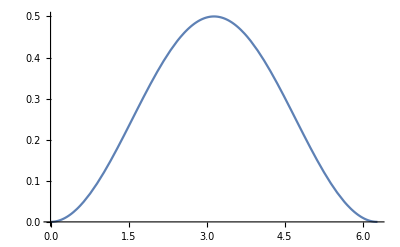

```mathematica
Plot[zθMad,{θ,0, 2π}]
```

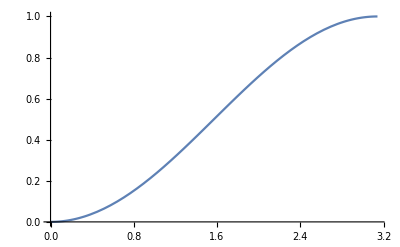

```mathematica
Plot[(1-Cos[θ])/2,{θ,0, π}]
```

Next steps
- Write up in methods section while checking all steps
- Test for a few specific cases 
- Figure out how to get a graph to read off the values it has for dG and tP 

- Solve for angular displacements

Testing 3D case of a +-polarized wave with a general looking vector v = {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]}

```mathematica
intR = FullSimplify[n[θ].Transpose[n[θ].ϵr] *1/RP[dG,tP, t,θ]](*rotated integrand. applying n^i n^j and then applying 1/Rp*)
```

(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
ϵ3d = FullSimplify[Rz[ϕ].Ry[-α].P.Transpose[Ry[-α]]].Transpose[Rz[ϕ]] //MatrixForm (*plus polarized wave in 3D*)
```

(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)

```mathematica
FullSimplify[ϵ3d]
```

(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | (1+Cos[α]^2) Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
(1+Cos[α]^2) Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]}
```

```mathematica
v[θ,ϕ].Transpose[v[θ,ϕ].ϵ3d] (*rotated integrand. applying v^i v^j and then applying 1/Rp*)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.(Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2 | Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | Cos[α] Cos[ϕ] Sin[α]
Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2 | Cos[α] Sin[α] Sin[ϕ]
Cos[α] Cos[ϕ] Sin[α] | Cos[α] Sin[α] Sin[ϕ] | Sin[α]^2)]

```mathematica
FullSimplify[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.Transpose[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.({{Cos[α]^2 Cos[ϕ]^2-Sin[ϕ]^2, Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ], Cos[α] Cos[ϕ] Sin[α]}, {Cos[ϕ] Sin[ϕ]+Cos[α]^2 Cos[ϕ] Sin[ϕ], -Cos[ϕ]^2+Cos[α]^2 Sin[ϕ]^2, Cos[α] Sin[α] Sin[ϕ]}, {Cos[α] Cos[ϕ] Sin[α], Cos[α] Sin[α] Sin[ϕ], Sin[α]^2}})]/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))]
```

Sin[α+θ]^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
FullSimplify[Sin[A[DP[tP,t], dG, θ]+θ]^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))]
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))]
```

-Sin[θ]^2/dG+(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2))

```mathematica
Manipulate[PolarPlot[-Sin[θ]^2/dG+(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)),{θ,0,2 π}],{dG,0.1,3},{tP,-0.1,5}]
```

#### Other polarizations in 2D

Plus-polarized wave rotated through an angle ϕ

```mathematica
P //MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Rz[ϕ].P.Transpose[Rz[ϕ]] // MatrixForm
```

(Cos[ϕ]^2-Sin[ϕ]^2 | 2 Cos[ϕ] Sin[ϕ] | 0
2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Sin[ϕ]^2 | 0
0 | 0 | 0)

```mathematica
Εr[α_] := FullSimplify[Ry[-α].Rz[ϕ].P.Transpose[Rz[ϕ]].Transpose[Ry[-α]]] (*Polarization of a x GW at an angle α*)
Εr[α] //MatrixForm
```

(Cos[α]^2 Cos[2 ϕ] | Cos[α] Sin[2 ϕ] | Cos[α] Cos[2 ϕ] Sin[α]
Cos[α] Sin[2 ϕ] | -Cos[2 ϕ] | Sin[α] Sin[2 ϕ]
Cos[α] Cos[2 ϕ] Sin[α] | Sin[α] Sin[2 ϕ] | Cos[2 ϕ] Sin[α]^2)

```mathematica
ϵr = Εr[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵr] //MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | -Cos[2 ϕ] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | ((t-tP)^2 Cos[2 ϕ] Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
intR = FullSimplify[n[θ].Transpose[n[θ].ϵr] *1/RP[dG,tP, t,θ]](*rotated integrand. applying n^i n^j and then applying 1/Rp*)
```

(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2)) ](*taking the difference manually*)
```

-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2))

```mathematica
Zr[θ_, ϕ_, dG_, tP_] := -1/2*(-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))
```

```mathematica
Manipulate[SphericalPlot3D[Zr[θ, ϕ, dG, tP],{θ,0,π},{ϕ,0,2 π}, PlotRange->All],{dG,0.01,10.},{tP,0.01,10.}]
```

```mathematica
(*why is this such a larger amplitude? This is not a 3D plot, it's for a general GW in a 2D geometry*)
```

```mathematica
zMad = 1/4*2Cos[2ϕ]*(1-Cos[θ]); (*Madison's full equation*)
```

```mathematica
SphericalPlot3D[zMad,{θ,0,π},{ϕ,0,2 π}, PlotRange->All]
```

-Graphics3D-

Cross-polarized wave

```mathematica
X //MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a x GW at an angle α*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = Εx[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵx] //MatrixForm
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
Εx = ϵx*1/RP[dG,tP, t,θ];
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].Εx] ](*applying n^i n^j and then applying 1/Rp*)
```

0

Getting 0 for some reason?

### (Updated approach) Redshift of + polarized rotated metric in 2D

```mathematica
P // MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
hg = FullSimplify[Ry[A[DP[tP,t], dG, θ]].Rz[ω].(P/RP[dG,tP, t,θ]).Transpose[Rz[ω]].Transpose[Ry[A[DP[tP,t], dG, θ]]]] // MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | Piecewise[{{-(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | (Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
Piecewise[{{-(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | -Cos[2 ω]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | Piecewise[{{((-t+tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}]
(Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | Piecewise[{{((-t+tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}] | ((t-tP)^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
hg1 = ({{((dG+(t-tP) Cos[θ])^2 Cos[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), -(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {-(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -Cos[2 ω]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), ((-t+tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])}, {(Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), ((-t+tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), ((t-tP)^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}}); (*if conditions, they're all the same*)
```

```mathematica
hg2 = ({{((dG+(t-tP) Cos[θ])^2 Cos[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), (Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {(Abs[dG+(t-tP) Cos[θ]] Sin[2 ω])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), -Cos[2 ω]/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), ((t-tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]])}, {(Cos[2 ω] Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), ((t-tP) Sin[θ] Sin[2 ω])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), ((t-tP)^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}});(*remaining true conditions*)
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hg1]]
```

((dG+2 (t-tP) Cos[θ])^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hg2]] (*give the same result*)
```

((dG+2 (t-tP) Cos[θ])^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
Hg[ω_,t_] := ((dG+2 (t-tP) Cos[θ])^2 Cos[2 ω] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
```

```mathematica
FullSimplify[Hg[ω,Tmin[tG, tP, dG,θ]] - Hg[ω,tP]]
```

(-1/dG+(8 (dG+tP)^2 (dG+tP-dG Cos[θ]) (dG-(dG+tP) Cos[θ])^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Cos[2 ω] Sin[θ]^2

```mathematica
Zg[θ_, dG_, tP_, hM_,ω_] := -(hM* dG)/2 (-1/dG+(8 (dG+tP)^2 (dG+tP-dG Cos[θ]) (dG-(dG+tP) Cos[θ])^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)) Sin[θ]^2 Cos[2 ω]
```

```mathematica
(*test the above function*)
```

```mathematica
Manipulate[Labeled[Plot[Zg[θ,dG,tP, h0/dG,ω π],{θ,0,π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ω = ",NumberForm[ω,{3,2}],", h0 = ",NumberForm[h0,{3,2}]}],Top],{h0,1,2},{dG,0.1,50},{tP,0.01,50}, {ω, 0, 2}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[Zg[θ,dG,tP, h0/dG,ω ],{θ,0,π},{ω,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", h0 = ",NumberForm[h0,{3,2}]}],Top],{h0,1,2},{dG,0.1,50},{tP,0.01,50}]
```

I think it goes to 0 for a x-polarized wave because a x-polarized wave doesn’t affect particles on the x/y axes (I think)

### Deflection angle in 2D

```mathematica
h // MatrixForm
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
n[θ]
```

{Sin[θ],0,Cos[θ]}

```mathematica
H[t_] := ({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}})
```

First two terms

```mathematica
H[tP] // MatrixForm
```

(1/(√(dG^2)) | 0 | 0
0 | -1/(√(dG^2)) | 0
0 | 0 | 0)

```mathematica
t1 = n[θ].H[tP] (*term 1*)
```

{Sin[θ]/(√(dG^2)),0,0}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].H[tP]]]
```

Sin[θ]^2/dG

```mathematica
t2 = Sin[θ]^2/dG n[θ]
```

{Sin[θ]^3/dG,0,(Cos[θ] Sin[θ]^2)/dG}

```mathematica
FullSimplify[t1-t2]
```

{(Cos[θ]^2 Sin[θ])/dG,0,-(Cos[θ] Sin[θ]^2)/dG}

n^k n^j applied to time derivative

```mathematica
FullSimplify[n[θ].Transpose[n[θ].H[t]]]
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
Hint[t_] := (dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
```

```mathematica
Hint[t] - Hint[tP]
```

-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
∫_tP^Tmin[tG, tP, dG,θ] (Hint[t] - Hint[tP])ⅆt
```

ConditionalExpression[(((tP (2 dG+tP))/(dG+tP-dG Cos[θ])+(2 dG^3 tP (4 dG+tP Csc[θ/2]^2))/(-2 dG^2 (2 dG^2+2 dG tP+tP^2)+4 dG^3 (dG+tP) Cos[θ])) Sin[θ]^2)/(2 dG), ]

Spatial Derivatives

```mathematica
H[t_] // MatrixForm
```

((dG+Cos[θ] (-tP+t_))^2/((dG^2+2 dG Cos[θ] (-tP+t_)+(-tP+t_)^2)^(3/2)) | 0 | -((-tP+t_) (dG+Cos[θ] (-tP+t_)) Sin[θ])/((dG^2+2 dG Cos[θ] (-tP+t_)+(-tP+t_)^2)^(3/2))
0 | -1/(√(dG^2+2 dG Cos[θ] (-tP+t_)+(-tP+t_)^2)) | 0
-((-tP+t_) (dG+Cos[θ] (-tP+t_)) Sin[θ])/((dG^2+2 dG Cos[θ] (-tP+t_)+(-tP+t_)^2)^(3/2)) | 0 | ((-tP+t_)^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+t_)+(-tP+t_)^2)^(3/2)))

```mathematica
H[tP]// MatrixForm
```

(1/(√(dG^2)) | 0 | 0
0 | -1/(√(dG^2)) | 0
0 | 0 | 0)

```mathematica
Z[dP_, θ_] := dP Cos[θ]
```

```mathematica
Z[DP[tP, t] ,θ] (*t-> tP-z Sec[θ]*)
```

(-t+tP) Cos[θ]

x = (-t + tP) Sin[θ]
t = tP-z Csc[θ]

```mathematica
H[tP-z Sec[θ]]// MatrixForm
```

((dG-z)^2/((dG^2-2 dG z+z^2 Sec[θ]^2)^(3/2)) | 0 | ((dG-z) z Tan[θ])/((dG^2-2 dG z+z^2 Sec[θ]^2)^(3/2))
0 | -1/(√(dG^2-2 dG z+z^2 Sec[θ]^2)) | 0
((dG-z) z Tan[θ])/((dG^2-2 dG z+z^2 Sec[θ]^2)^(3/2)) | 0 | (z^2 Tan[θ]^2)/((dG^2-2 dG z+z^2 Sec[θ]^2)^(3/2)))

```mathematica
Zmax[tG_, tP_, dG_,θ_] = Tmin[tG, tP, dG,θ]*Cos[θ];
```

```mathematica
FullSimplify[H[tP-Zmax[tG, tP, dG,θ]* Sec[θ]]]// MatrixForm
```

((dG+(tP Cos[θ] (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ]))^2/((dG^2+(tP^2 (tP-2 dG Cos[θ])^2)/(4 (dG+tP-dG Cos[θ])^2)+(dG tP Cos[θ] (-tP+2 dG Cos[θ]))/(dG+tP-dG Cos[θ]))^(3/2)) | 0 | (tP (tP-2 dG Cos[θ]) (dG+(tP Cos[θ] (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ])/(2 (dG+tP-dG Cos[θ]) (dG^2+(tP^2 (tP-2 dG Cos[θ])^2)/(4 (dG+tP-dG Cos[θ])^2)+(dG tP Cos[θ] (-tP+2 dG Cos[θ]))/(dG+tP-dG Cos[θ]))^(3/2))
0 | -1/(√(dG^2+(tP^2 (tP-2 dG Cos[θ])^2)/(4 (dG+tP-dG Cos[θ])^2)+(dG tP Cos[θ] (-tP+2 dG Cos[θ]))/(dG+tP-dG Cos[θ]))) | 0
(tP (tP-2 dG Cos[θ]) (dG+(tP Cos[θ] (tP-2 dG Cos[θ]))/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ])/(2 (dG+tP-dG Cos[θ]) (dG^2+(tP^2 (tP-2 dG Cos[θ])^2)/(4 (dG+tP-dG Cos[θ])^2)+(dG tP Cos[θ] (-tP+2 dG Cos[θ]))/(dG+tP-dG Cos[θ]))^(3/2)) | 0 | (tP^2 (tP-2 dG Cos[θ])^2 Sin[θ]^2)/(4 (dG+tP-dG Cos[θ])^2 (dG^2+(tP^2 (tP-2 dG Cos[θ])^2)/(4 (dG+tP-dG Cos[θ])^2)+(dG tP Cos[θ] (-tP+2 dG Cos[θ]))/(dG+tP-dG Cos[θ]))^(3/2)))

```mathematica
∫_0^Zmax[tG, tP, dG,θ] (H[tP-z Sec[θ]] - Hint[tP])ⅆz
```

```mathematica
Xmax[tG_, tP_, dG_,θ_] = Tmin[tG, tP, dG,θ]*Sin[θ];
```

```mathematica
∫_0^Xmax[tG, tP, dG,θ] (H[tP-z Csc[θ]] - Hint[tP])ⅆz
```

```mathematica
FullSimplify[h] //MatrixForm
```

(1/(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
Subscript[h, x]= D[DP[tP,t]Cos[θ] h,θ] ; (*x = dP Sin[θ] so dx = dP Cos[θ] dθ ?*) (*check Rp versus dp!!*)
Subscript[h, y]=0 ; 
Subscript[h, z]= D[-DP[tP,t]Sin[θ] h,θ] ; (*z = dP Cos[θ] so dz = -dP Sin[θ] dθ ?*)
FullSimplify[Subscript[h, x]] //MatrixForm
FullSimplify[Subscript[h, z]] //MatrixForm
```

(((t-tP) (dG+(t-tP) Cos[θ]) (3 (dG^2+(t-tP)^2) (t-tP) Cos[θ]+dG (dG^2+3 (t-tP)^2+2 (t-tP)^2 Cos[2 θ])) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Sin[θ] | 0
((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | -((t-tP)^3 (6 dG (t-tP) Cos[θ]+(dG^2+(t-tP)^2) (1+3 Cos[2 θ])+2 dG (t-tP) Cos[3 θ]) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

(((t-tP) (Cos[θ]+((t-tP)^2 (-2 t+2 tP-dG Cos[θ]+(t-tP) Cos[θ]^2) Sin[θ]^2)/(dG+(t-tP) Cos[θ])^3))/((1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)^2) | 0 | -((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Cos[θ] | 0
-((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^3 (3 (dG^2+(t-tP)^2) Cos[θ]+2 dG (t-tP) (2+Cos[2 θ])) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

```mathematica
Integrate[Subscript[h, x],{t,Tmin[tG, tP, dG,θ],tP}]
```

ConditionalExpression[(h0 (2 dG^2+2 dG tP+2 dG^2 Cos[θ]-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ])) (Cos[θ]+ⅈ Sin[θ]))/(dG (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])), ]

$Aborted

(Sin[θ] Sin[ϕ] ((4. (t-1. tP)^2 Cos[ϕ] Sin[θ] (2. dG^2+dG (4. t-4. tP) Cos[θ]+(2. t^2-4. t tP+2. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2))/((dG^2+dG (2. t-2. tP) Cos[θ]+(t^2-2. t tP+tP^2) Cos[θ]^2+(t^2-2. t tP+tP^2) Cos[ϕ]^2 Sin[θ]^2)^2)+((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(dG+(t-tP) Cos[θ])))/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))==0